```mathematica
toCWPair[i_Integer]:=Module[{b=Rest@IntegerDigits[i,2],t={1,1}},
Scan[If[#==0,t={First[t],Plus@@t},t={Plus@@t,Last[t]}]&,b];
t];
```

```mathematica
toPPT[{v_,u_}]:={u^2-v^2,2u v,u^2+v^2}
```

```mathematica
Row[{#,If[OddQ[#[[1]]&&OddQ[#[[2]]]],Style[#,Red],#]&[toCWPair[#]],toPPT[toCWPair[#]]},":"]& /@ (2Range[25])//Column
```

::2{1,2}{3,4,5}
::4{1,3}{8,6,10}
::6{2,3}{5,12,13}
::8{1,4}{15,8,17}
::10{3,5}{16,30,34}
::12{2,5}{21,20,29}
::14{3,4}{7,24,25}
::16{1,5}{24,10,26}
::18{4,7}{33,56,65}
::20{3,8}{55,48,73}
::22{5,7}{24,70,74}
::24{2,7}{45,28,53}
::26{5,8}{39,80,89}
::28{3,7}{40,42,58}
::30{4,5}{9,40,41}
::32{1,6}{35,12,37}
::34{5,9}{56,90,106}
::36{4,11}{105,88,137}
::38{7,10}{51,140,149}
::40{3,11}{112,66,130}
::42{8,13}{105,208,233}
::44{5,12}{119,120,169}
::46{7,9}{32,126,130}
::48{2,9}{77,36,85}
::50{7,12}{95,168,193}

```mathematica
If[OddQ[#[[1]]&&OddQ[#[[2]]]],Null,Row[{#,":",toPPT[#]}]]&[toCWPair[#]]& /@ (2Range[25])//Column
```

{1,2}:{3,4,5}

{2,3}:{5,12,13}
{1,4}:{15,8,17}

{2,5}:{21,20,29}
{3,4}:{7,24,25}

{4,7}:{33,56,65}
{3,8}:{55,48,73}

{2,7}:{45,28,53}
{5,8}:{39,80,89}

{4,5}:{9,40,41}
{1,6}:{35,12,37}

{4,11}:{105,88,137}
{7,10}:{51,140,149}

{8,13}:{105,208,233}
{5,12}:{119,120,169}

{2,9}:{77,36,85}
{7,12}:{95,168,193}

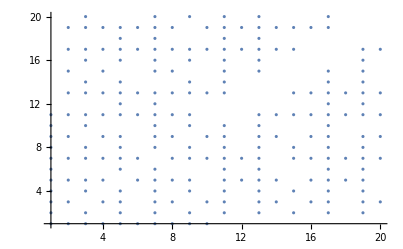

```mathematica
ListPlot[toCWPair /@ (Range[2000]),PlotRange->{{1,20},{1,20}}]
```

### More

```mathematica
FindSequenceFunction[{2,6,8,12,14,18,20,24,26},n]
```

1/2 (-1)^n (1-(-1)^n+6 (-1)^n n)

```mathematica
Table[1/2 (-1)^n (1-(-1)^n+6 (-1)^n n),{n,1,20}]
```

{2,6,8,12,14,18,20,24,26,30,32,36,38,42,44,48,50,54,56,60}

```mathematica
FullSimplify[1/2 (-1)^n (1-(-1)^n+6 (-1)^n n)]
```

1/2 (-1)^n (1+(-1)^n (-1+6 n))

```mathematica
f[n_]:=1/2 (-1)^n (1-(-1)^n+6 (-1)^n n)
```

```mathematica
f /@ Range[25]
```

{2,6,8,12,14,18,20,24,26,30,32,36,38,42,44,48,50,54,56,60,62,66,68,72,74}

```mathematica
toCWPair /@ (f /@ Range[25])//Column
```

{1,2}
{2,3}
{1,4}
{2,5}
{3,4}
{4,7}
{3,8}
{2,7}
{5,8}
{4,5}
{1,6}
{4,11}
{7,10}
{8,13}
{5,12}
{2,9}
{7,12}
{8,11}
{3,10}
{4,9}
{5,6}
{6,11}
{5,14}
{4,15}
{11,18}

```mathematica
toPPT /@ (toCWPair /@ (f /@ Range[25]))//Column
```

{3,4,5}
{5,12,13}
{15,8,17}
{21,20,29}
{7,24,25}
{33,56,65}
{55,48,73}
{45,28,53}
{39,80,89}
{9,40,41}
{35,12,37}
{105,88,137}
{51,140,149}
{105,208,233}
{119,120,169}
{77,36,85}
{95,168,193}
{57,176,185}
{91,60,109}
{65,72,97}
{11,60,61}
{85,132,157}
{171,140,221}
{209,120,241}
{203,396,445}

```mathematica
fromIndexToPPT[n_] := toPPT@toCWPair@f@n
```

```mathematica
fromIndexToPPT[100]
```

{1525,1548,2173}

```mathematica
fromIndexToPPT /@ Range[25] //Column
```

{3,4,5}
{5,12,13}
{15,8,17}
{21,20,29}
{7,24,25}
{33,56,65}
{55,48,73}
{45,28,53}
{39,80,89}
{9,40,41}
{35,12,37}
{105,88,137}
{51,140,149}
{105,208,233}
{119,120,169}
{77,36,85}
{95,168,193}
{57,176,185}
{91,60,109}
{65,72,97}
{11,60,61}
{85,132,157}
{171,140,221}
{209,120,241}
{203,396,445}

```mathematica
1300 .12
```

```mathematica
156./30^2
```

0.173333

```mathematica
Manipulate[
plotlabel="The first "<>ToString[n]<>" Primitive Pythagorean Triples {A,B,C}";
Switch[
mode,
5, (* list of {A,B,C} *)
Pane[fromIndexToPPT/@Range[n],plotlabel,Scrollbars->{False,Automatic},ImageSize->{600,350}],
4,  (* 3D plot of {A,B,C} *)
ListPointPlot3D[labeled[#]& /@ (fromIndexToPPT/@Range[n]),AxesLabel->{"A","B","C"},PlotLabel->plotlabel,ImageSize->{600,350}],
_, (* 2D plots *)
ListPlot[labeled[Switch[mode,1,Most,2,#[[{1,3}]]&,3,Rest][#],#]& /@ (fromIndexToPPT/@Range[n]),
AxesLabel->Switch[mode,1,{"A","B"},2,{"A","C"},3,{"B","C"}],
PlotLabel->"The first "<>ToString[n]<>" Primitive Pythagorean Triples {A,B,C}",ImageSize->{600,350}]
],
{{n,10},1,200,1,ControlPlacement->Top},
{mode,{1->"graph AB",2->"graph AC",3->"graph BC",4->"graph ABC",5->"list {A,B,C}"},ControlPlacement->Top},
{labeled,{Tooltip,Labeled},ControlPlacement->Top},
{plotlabel,{},ControlType->None}
]
```

```mathematica
Manipulate[
plotlabel="The first "<>ToString[n]<>" Primitive Pythagorean Triples {A,B,C}";
Switch[
mode,
5, (* list of {A,B,C} *)
Pane[fromIndexToPPT/@Range[n],plotlabel,Scrollbars->{False,Automatic},ImageSize->{600,350}],
4,  (* 3D plot of {A,B,C} *)
ListPointPlot3D[labeled[#]& /@ (fromIndexToPPT/@Range[n]),AxesLabel->{"A","B","C"},PlotLabel->plotlabel,ImageSize->{600,350}],
_, (* 2D plots *)
ListPlot[labeled[Switch[mode,1,Most,2,#[[{1,3}]]&,3,Rest][#],#]& /@ (fromIndexToPPT/@Range[n]),
AxesLabel->Switch[mode,1,{"A","B"},2,{"A","C"},3,{"B","C"}],
PlotLabel->"The first "<>ToString[n]<>" Primitive Pythagorean Triples {A,B,C}",ImageSize->{600,350}]
],
{{n,10},1,200,1,ControlPlacement->Top},
{mode,{1->"graph AB",2->"graph AC",3->"graph BC",4->"graph ABC",5->"list {A,B,C}"},ControlPlacement->Top},
{labeled,{Tooltip,Labeled},ControlPlacement->Top},
{plotlabel,{},ControlType->None}
]
```

### PPT generation from algorithm in Colton's paper

https://knowledge.e.southern.edu/cgi/viewcontent.cgi?article=1000&context=physics_studentresearch

```mathematica
Clear[NetSummary];
Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];
NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];
NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

```mathematica
{{3,4,5},{5,12,13}} ~Union~ 
NetSummary[{4n+3,8n^2+12n+4,8n^2+12n+5},{4n+4,4n^2+8n+3,4n^2+8n+5},{4n+5,8n^2+20n+12,8n^2+20n+13},{n,1,∞}]
```

{{3,4,5},{5,12,13}}∪𝕊_(n=1)^∞[{4 n+3,8 n^2+12 n+4,8 n^2+12 n+5},{4 n+4,4 n^2+8 n+3,4 n^2+8 n+5},{4 n+5,8 n^2+20 n+12,8 n^2+20 n+13}]

```mathematica
ExpandAll@NetSummary[{4n+3,8n^2+12n+4,8n^2+12n+5},{4n+4,4n^2+8n+3,4n^2+8n+5},{4n+5,8n^2+20n+12,8n^2+20n+13},{n,0,10}]//Column
```

{3,4,5}
{4,3,5}
{5,12,13}
{7,24,25}
{8,15,17}
{9,40,41}
{11,60,61}
{12,35,37}
{13,84,85}
{15,112,113}
{16,63,65}
{17,144,145}
{19,180,181}
{20,99,101}
{21,220,221}
{23,264,265}
{24,143,145}
{25,312,313}
{27,364,365}
{28,195,197}
{29,420,421}
{31,480,481}
{32,255,257}
{33,544,545}
{35,612,613}
{36,323,325}
{37,684,685}
{39,760,761}
{40,399,401}
{41,840,841}
{43,924,925}
{44,483,485}
{45,1012,1013}

```mathematica
algebraic={{3,4,5},{5,12,13}} ~Union~ ExpandAll@NetSummary[{4n+3,8n^2+12n+4,8n^2+12n+5},{4n+4,4n^2+8n+3,4n^2+8n+5},{4n+5,8n^2+20n+12,8n^2+20n+13},{n,1,45}]
```

{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{17,144,145},{19,180,181},{20,99,101},{21,220,221},{23,264,265},{24,143,145},{25,312,313},{27,364,365},{28,195,197},{29,420,421},{31,480,481},{32,255,257},{33,544,545},{35,612,613},{36,323,325},{37,684,685},{39,760,761},{40,399,401},{41,840,841},{43,924,925},{44,483,485},{45,1012,1013},{47,1104,1105},{48,575,577},{49,1200,1201},{51,1300,1301},{52,675,677},{53,1404,1405},{55,1512,1513},{56,783,785},{57,1624,1625},{59,1740,1741},{60,899,901},{61,1860,1861},{63,1984,1985},{64,1023,1025},{65,2112,2113},{67,2244,2245},{68,1155,1157},{69,2380,2381},{71,2520,2521},{72,1295,1297},{73,2664,2665},{75,2812,2813},{76,1443,1445},{77,2964,2965},{79,3120,3121},{80,1599,1601},{81,3280,3281},{83,3444,3445},{84,1763,1765},{85,3612,3613},{87,3784,3785},{88,1935,1937},{89,3960,3961},{91,4140,4141},{92,2115,2117},{93,4324,4325},{95,4512,4513},{96,2303,2305},{97,4704,4705},{99,4900,4901},{100,2499,2501},{101,5100,5101},{103,5304,5305},{104,2703,2705},{105,5512,5513},{107,5724,5725},{108,2915,2917},{109,5940,5941},{111,6160,6161},{112,3135,3137},{113,6384,6385},{115,6612,6613},{116,3363,3365},{117,6844,6845},{119,7080,7081},{120,3599,3601},{121,7320,7321},{123,7564,7565},{124,3843,3845},{125,7812,7813},{127,8064,8065},{128,4095,4097},{129,8320,8321},{131,8580,8581},{132,4355,4357},{133,8844,8845},{135,9112,9113},{136,4623,4625},{137,9384,9385},{139,9660,9661},{140,4899,4901},{141,9940,9941},{143,10224,10225},{144,5183,5185},{145,10512,10513},{147,10804,10805},{148,5475,5477},{149,11100,11101},{151,11400,11401},{152,5775,5777},{153,11704,11705},{155,12012,12013},{156,6083,6085},{157,12324,12325},{159,12640,12641},{160,6399,6401},{161,12960,12961},{163,13284,13285},{164,6723,6725},{165,13612,13613},{167,13944,13945},{168,7055,7057},{169,14280,14281},{171,14620,14621},{172,7395,7397},{173,14964,14965},{175,15312,15313},{176,7743,7745},{177,15664,15665},{179,16020,16021},{180,8099,8101},{181,16380,16381},{183,16744,16745},{184,8463,8465},{185,17112,17113}}

```mathematica
Length@%
```

137

```mathematica
enumerated=Sort@Drop[Sort /@ ({{3,4,5},{5,12,13},{15,8,17},{21,20,29},{7,24,25},{33,56,65},{55,48,73},{45,28,53},{39,80,89},{9,40,41},{35,12,37},{105,88,137},{51,140,149},{105,208,233},{119,120,169},{77,36,85},{95,168,193},{57,176,185},{91,60,109},{65,72,97},{11,60,61},{85,132,157},{171,140,221},{209,120,241},{203,396,445},{69,260,269},{187,84,205},{377,336,505},{155,468,493},{217,456,505},{207,224,305},{117,44,125},{175,288,337},{145,408,433},{299,180,349},{297,304,425},{75,308,317},{189,340,389},{275,252,373},{153,104,185},{115,252,277},{13,84,85},{63,16,65},{253,204,325},{135,352,377},{333,644,725},{403,396,565},{345,152,377},{451,780,901},{301,900,949},{527,336,625},{429,460,629},{87,416,425},{429,700,821},{779,660,1021},{777,464,905},{715,1428,1597},{205,828,853},{459,220,509},{817,744,1105},{315,988,1037},{369,800,881},{319,360,481},{165,52,173},{279,440,521},{273,736,785},{627,364,725},{697,696,985},{195,748,773},{637,1116,1285},{987,884,1325},{665,432,793},{539,1140,1261},{93,476,485},{247,96,265},{629,540,829},{287,816,865},{517,1044,1165},{555,572,797},{273,136,305},{315,572,653},{165,532,557},{231,160,281},{133,156,205},{15,112,113},{161,240,289},{351,280,449},{493,276,565},{495,952,1073},{185,672,697},{551,240,601},{1173,1036,1565},{495,1472,1553},{741,1540,1709},{731,780,1069},{513,184,545},{795,1292,1517},{693,1924,2045},{1479,880,1721},{1525,1548,2173},{399,1600,1649},{1105,1968,2257},{1647,1496,2225},{989,660,1189},{767,1656,1825},{105,608,617},{391,120,409},{1325,1092,1717},{671,1800,1921},{1501,2940,3301},{1755,1748,2477},{1305,592,1433},{1659,2900,3341},{1053,3196,3365},{1767,1144,2105},{1357,1476,2005},{255,1288,1313},{1037,1716,2005},{1827,1564,2405},{1705,1032,1993},{1539,3100,3461},{413,1716,1765},{851,420,949},{1425,1312,1937},{531,1700,1781},{561,1240,1361},{455,528,697},{221,60,229},{407,624,745},{441,1160,1241},{1075,612,1237},{1265,1248,1777},{371,1380,1429},{1349,2340,2701},{2139,1900,2861},{1537,984,1825},{1275,2668,2957},{245,1188,1213},{759,280,809}}), -2]
```

{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{20,21,29},{28,45,53},{33,56,65},{36,77,85},{39,80,89},{44,117,125},{48,55,73},{51,140,149},{52,165,173},{57,176,185},{60,91,109},{60,221,229},{65,72,97},{69,260,269},{75,308,317},{84,187,205},{85,132,157},{87,416,425},{88,105,137},{93,476,485},{95,168,193},{96,247,265},{104,153,185},{105,208,233},{105,608,617},{115,252,277},{119,120,169},{120,209,241},{120,391,409},{133,156,205},{135,352,377},{136,273,305},{140,171,221},{145,408,433},{152,345,377},{155,468,493},{160,231,281},{161,240,289},{165,532,557},{175,288,337},{180,299,349},{184,513,545},{185,672,697},{189,340,389},{195,748,773},{203,396,445},{204,253,325},{205,828,853},{207,224,305},{217,456,505},{220,459,509},{240,551,601},{252,275,373},{255,1288,1313},{273,736,785},{276,493,565},{279,440,521},{280,351,449},{287,816,865},{297,304,425},{301,900,949},{315,572,653},{315,988,1037},{319,360,481},{333,644,725},{336,377,505},{336,527,625},{364,627,725},{369,800,881},{371,1380,1429},{396,403,565},{399,1600,1649},{407,624,745},{413,1716,1765},{420,851,949},{429,460,629},{429,700,821},{432,665,793},{441,1160,1241},{451,780,901},{455,528,697},{464,777,905},{495,952,1073},{495,1472,1553},{517,1044,1165},{531,1700,1781},{539,1140,1261},{540,629,829},{555,572,797},{561,1240,1361},{592,1305,1433},{612,1075,1237},{637,1116,1285},{660,779,1021},{660,989,1189},{671,1800,1921},{693,1924,2045},{696,697,985},{715,1428,1597},{731,780,1069},{741,1540,1709},{744,817,1105},{767,1656,1825},{795,1292,1517},{880,1479,1721},{884,987,1325},{984,1537,1825},{1032,1705,1993},{1036,1173,1565},{1037,1716,2005},{1053,3196,3365},{1092,1325,1717},{1105,1968,2257},{1144,1767,2105},{1248,1265,1777},{1275,2668,2957},{1312,1425,1937},{1349,2340,2701},{1357,1476,2005},{1496,1647,2225},{1501,2940,3301},{1525,1548,2173},{1539,3100,3461},{1564,1827,2405},{1659,2900,3341},{1748,1755,2477},{1900,2139,2861}}

```mathematica
Transpose@{algebraic,enumerated} //MatrixForm
```

Transpose[{{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{17,144,145},{19,180,181},{20,99,101},{21,220,221},{23,264,265},{24,143,145},{25,312,313},{27,364,365},{28,195,197},{29,420,421},{31,480,481},{32,255,257},{33,544,545},{35,612,613},{36,323,325},{37,684,685},{39,760,761},{40,399,401},{41,840,841},{43,924,925},{44,483,485},{45,1012,1013},{47,1104,1105},{48,575,577},{49,1200,1201},{51,1300,1301},{52,675,677},{53,1404,1405},{55,1512,1513},{56,783,785},{57,1624,1625},{59,1740,1741},{60,899,901},{61,1860,1861},{63,1984,1985},{64,1023,1025},{65,2112,2113},{67,2244,2245},{68,1155,1157},{69,2380,2381},{71,2520,2521},{72,1295,1297},{73,2664,2665},{75,2812,2813},{76,1443,1445},{77,2964,2965},{79,3120,3121},{80,1599,1601},{81,3280,3281},{83,3444,3445},{84,1763,1765},{85,3612,3613},{87,3784,3785},{88,1935,1937},{89,3960,3961},{91,4140,4141},{92,2115,2117},{93,4324,4325},{95,4512,4513},{96,2303,2305},{97,4704,4705},{99,4900,4901},{100,2499,2501},{101,5100,5101},{103,5304,5305},{104,2703,2705},{105,5512,5513},{107,5724,5725},{108,2915,2917},{109,5940,5941},{111,6160,6161},{112,3135,3137},{113,6384,6385},{115,6612,6613},{116,3363,3365},{117,6844,6845},{119,7080,7081},{120,3599,3601},{121,7320,7321},{123,7564,7565},{124,3843,3845},{125,7812,7813},{127,8064,8065},{128,4095,4097},{129,8320,8321},{131,8580,8581},{132,4355,4357},{133,8844,8845},{135,9112,9113},{136,4623,4625},{137,9384,9385},{139,9660,9661},{140,4899,4901},{141,9940,9941},{143,10224,10225},{144,5183,5185},{145,10512,10513},{147,10804,10805},{148,5475,5477},{149,11100,11101},{151,11400,11401},{152,5775,5777},{153,11704,11705},{155,12012,12013},{156,6083,6085},{157,12324,12325},{159,12640,12641},{160,6399,6401},{161,12960,12961},{163,13284,13285},{164,6723,6725},{165,13612,13613},{167,13944,13945},{168,7055,7057},{169,14280,14281},{171,14620,14621},{172,7395,7397},{173,14964,14965},{175,15312,15313},{176,7743,7745},{177,15664,15665},{179,16020,16021},{180,8099,8101},{181,16380,16381},{183,16744,16745},{184,8463,8465},{185,17112,17113}},{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{20,21,29},{28,45,53},{33,56,65},{36,77,85},{39,80,89},{44,117,125},{48,55,73},{51,140,149},{52,165,173},{57,176,185},{60,91,109},{65,72,97},{69,260,269},{75,308,317},{84,187,205},{85,132,157},{87,416,425},{88,105,137},{93,476,485},{95,168,193},{96,247,265},{104,153,185},{105,208,233},{115,252,277},{119,120,169},{120,209,241},{133,156,205},{135,352,377},{136,273,305},{140,171,221},{145,408,433},{152,345,377},{155,468,493},{160,231,281},{161,240,289},{165,532,557},{175,288,337},{180,299,349},{185,672,697},{189,340,389},{195,748,773},{203,396,445},{204,253,325},{205,828,853},{207,224,305},{217,456,505},{220,459,509},{252,275,373},{273,736,785},{276,493,565},{279,440,521},{280,351,449},{287,816,865},{297,304,425},{301,900,949},{315,572,653},{315,988,1037},{319,360,481},{333,644,725},{336,377,505},{336,527,625},{364,627,725},{369,800,881},{396,403,565},{429,460,629},{429,700,821},{432,665,793},{451,780,901},{464,777,905},{495,952,1073},{517,1044,1165},{539,1140,1261},{540,629,829},{555,572,797},{637,1116,1285},{660,779,1021},{696,697,985},{715,1428,1597},{744,817,1105},{884,987,1325}}}]

```mathematica
n=41;
While[FreeQ[fromIndexToPPT[n],185] ,n++];
{n,fromIndexToPPT[n]}
```

{90,{185,672,697}}

```mathematica
enumerated=Take[Sort[Sort /@ (fromIndexToPPT/@Range[50000])],137]
```

{{3,4,5},{5,12,13},{7,24,25},{8,15,17},{9,40,41},{11,60,61},{12,35,37},{13,84,85},{15,112,113},{16,63,65},{17,144,145},{19,180,181},{20,21,29},{20,99,101},{21,220,221},{23,264,265},{24,143,145},{25,312,313},{27,364,365},{28,45,53},{28,195,197},{29,420,421},{31,480,481},{32,255,257},{33,56,65},{33,544,545},{36,77,85},{36,323,325},{39,80,89},{44,117,125},{48,55,73},{51,140,149},{52,165,173},{57,176,185},{60,91,109},{60,221,229},{65,72,97},{68,285,293},{69,260,269},{75,308,317},{76,357,365},{84,187,205},{84,437,445},{85,132,157},{87,416,425},{88,105,137},{92,525,533},{93,476,485},{95,168,193},{96,247,265},{100,621,629},{104,153,185},{105,208,233},{105,608,617},{108,725,733},{111,680,689},{115,252,277},{116,837,845},{119,120,169},{120,209,241},{120,391,409},{123,836,845},{124,957,965},{129,920,929},{132,475,493},{133,156,205},{135,352,377},{136,273,305},{140,171,221},{141,1100,1109},{145,408,433},{147,1196,1205},{152,345,377},{155,468,493},{156,667,685},{159,1400,1409},{160,231,281},{161,240,289},{165,532,557},{165,1508,1517},{168,425,457},{168,775,793},{175,288,337},{177,1736,1745},{180,299,349},{183,1856,1865},{184,513,545},{185,672,697},{189,340,389},{192,1015,1033},{195,748,773},{195,2108,2117},{200,609,641},{201,2240,2249},{203,396,445},{204,253,325},{204,1147,1165},{205,828,853},{207,224,305},{213,2516,2525},{215,912,937},{216,713,745},{217,456,505},{219,2660,2669},{220,459,509},{225,272,353},{228,325,397},{228,1435,1453},{231,520,569},{231,2960,2969},{232,825,857},{235,1092,1117},{237,3116,3125},{240,551,601},{240,1591,1609},{245,1188,1213},{248,945,977},{249,3440,3449},{252,275,373},{255,1288,1313},{255,3608,3617},{259,660,709},{260,651,701},{261,380,461},{264,1073,1105},{264,1927,1945},{265,1392,1417},{273,736,785},{276,493,565},{279,440,521},{280,351,449},{280,759,809},{280,1209,1241},{285,1612,1637},{287,816,865},{295,1728,1753},{296,1353,1385}}

```mathematica
Transpose@{algebraic,enumerated} //MatrixForm
```

((3
4
5) | (3
4
5)
(5
12
13) | (5
12
13)
(7
24
25) | (7
24
25)
(8
15
17) | (8
15
17)
(9
40
41) | (9
40
41)
(11
60
61) | (11
60
61)
(12
35
37) | (12
35
37)
(13
84
85) | (13
84
85)
(15
112
113) | (15
112
113)
(16
63
65) | (16
63
65)
(17
144
145) | (17
144
145)
(19
180
181) | (19
180
181)
(20
99
101) | (20
21
29)
(21
220
221) | (20
99
101)
(23
264
265) | (21
220
221)
(24
143
145) | (23
264
265)
(25
312
313) | (24
143
145)
(27
364
365) | (25
312
313)
(28
195
197) | (27
364
365)
(29
420
421) | (28
45
53)
(31
480
481) | (28
195
197)
(32
255
257) | (29
420
421)
(33
544
545) | (31
480
481)
(35
612
613) | (32
255
257)
(36
323
325) | (33
56
65)
(37
684
685) | (33
544
545)
(39
760
761) | (36
77
85)
(40
399
401) | (36
323
325)
(41
840
841) | (39
80
89)
(43
924
925) | (44
117
125)
(44
483
485) | (48
55
73)
(45
1012
1013) | (51
140
149)
(47
1104
1105) | (52
165
173)
(48
575
577) | (57
176
185)
(49
1200
1201) | (60
91
109)
(51
1300
1301) | (60
221
229)
(52
675
677) | (65
72
97)
(53
1404
1405) | (68
285
293)
(55
1512
1513) | (69
260
269)
(56
783
785) | (75
308
317)
(57
1624
1625) | (76
357
365)
(59
1740
1741) | (84
187
205)
(60
899
901) | (84
437
445)
(61
1860
1861) | (85
132
157)
(63
1984
1985) | (87
416
425)
(64
1023
1025) | (88
105
137)
(65
2112
2113) | (92
525
533)
(67
2244
2245) | (93
476
485)
(68
1155
1157) | (95
168
193)
(69
2380
2381) | (96
247
265)
(71
2520
2521) | (100
621
629)
(72
1295
1297) | (104
153
185)
(73
2664
2665) | (105
208
233)
(75
2812
2813) | (105
608
617)
(76
1443
1445) | (108
725
733)
(77
2964
2965) | (111
680
689)
(79
3120
3121) | (115
252
277)
(80
1599
1601) | (116
837
845)
(81
3280
3281) | (119
120
169)
(83
3444
3445) | (120
209
241)
(84
1763
1765) | (120
391
409)
(85
3612
3613) | (123
836
845)
(87
3784
3785) | (124
957
965)
(88
1935
1937) | (129
920
929)
(89
3960
3961) | (132
475
493)
(91
4140
4141) | (133
156
205)
(92
2115
2117) | (135
352
377)
(93
4324
4325) | (136
273
305)
(95
4512
4513) | (140
171
221)
(96
2303
2305) | (141
1100
1109)
(97
4704
4705) | (145
408
433)
(99
4900
4901) | (147
1196
1205)
(100
2499
2501) | (152
345
377)
(101
5100
5101) | (155
468
493)
(103
5304
5305) | (156
667
685)
(104
2703
2705) | (159
1400
1409)
(105
5512
5513) | (160
231
281)
(107
5724
5725) | (161
240
289)
(108
2915
2917) | (165
532
557)
(109
5940
5941) | (165
1508
1517)
(111
6160
6161) | (168
425
457)
(112
3135
3137) | (168
775
793)
(113
6384
6385) | (175
288
337)
(115
6612
6613) | (177
1736
1745)
(116
3363
3365) | (180
299
349)
(117
6844
6845) | (183
1856
1865)
(119
7080
7081) | (184
513
545)
(120
3599
3601) | (185
672
697)
(121
7320
7321) | (189
340
389)
(123
7564
7565) | (192
1015
1033)
(124
3843
3845) | (195
748
773)
(125
7812
7813) | (195
2108
2117)
(127
8064
8065) | (200
609
641)
(128
4095
4097) | (201
2240
2249)
(129
8320
8321) | (203
396
445)
(131
8580
8581) | (204
253
325)
(132
4355
4357) | (204
1147
1165)
(133
8844
8845) | (205
828
853)
(135
9112
9113) | (207
224
305)
(136
4623
4625) | (213
2516
2525)
(137
9384
9385) | (215
912
937)
(139
9660
9661) | (216
713
745)
(140
4899
4901) | (217
456
505)
(141
9940
9941) | (219
2660
2669)
(143
10224
10225) | (220
459
509)
(144
5183
5185) | (225
272
353)
(145
10512
10513) | (228
325
397)
(147
10804
10805) | (228
1435
1453)
(148
5475
5477) | (231
520
569)
(149
11100
11101) | (231
2960
2969)
(151
11400
11401) | (232
825
857)
(152
5775
5777) | (235
1092
1117)
(153
11704
11705) | (237
3116
3125)
(155
12012
12013) | (240
551
601)
(156
6083
6085) | (240
1591
1609)
(157
12324
12325) | (245
1188
1213)
(159
12640
12641) | (248
945
977)
(160
6399
6401) | (249
3440
3449)
(161
12960
12961) | (252
275
373)
(163
13284
13285) | (255
1288
1313)
(164
6723
6725) | (255
3608
3617)
(165
13612
13613) | (259
660
709)
(167
13944
13945) | (260
651
701)
(168
7055
7057) | (261
380
461)
(169
14280
14281) | (264
1073
1105)
(171
14620
14621) | (264
1927
1945)
(172
7395
7397) | (265
1392
1417)
(173
14964
14965) | (273
736
785)
(175
15312
15313) | (276
493
565)
(176
7743
7745) | (279
440
521)
(177
15664
15665) | (280
351
449)
(179
16020
16021) | (280
759
809)
(180
8099
8101) | (280
1209
1241)
(181
16380
16381) | (285
1612
1637)
(183
16744
16745) | (287
816
865)
(184
8463
8465) | (295
1728
1753)
(185
17112
17113) | (296
1353
1385))

### Counter-example to the claim that the algebraic method generates all PPTs

```mathematica
{{({{20}, {21}, {29}})}, {({{20}, {99}, {101}})}}  {{({{28}, {45}, {53}})}, {({{28}, {195}, {197}})}}   {{({{36}, {77}, {85}})}, {({{36}, {323}, {325}})}}   {{({{44}, {117}, {125}})}, {({{44}, {483}, {485}})}}
```

## Understanding the "algebraic method":

```mathematica
Clear[n];{{4n+3,8n^2+12n+4,8n^2+12n+5},{4n+4,4n^2+8n+3,4n^2+8n+5},{4n+5,8n^2+20n+12,8n^2+20n+13}}
```

{{4 n+3,8 n^2+12 n+4,8 n^2+12 n+5},{4 n+4,4 n^2+8 n+3,4 n^2+8 n+5},{4 n+5,8 n^2+20 n+12,8 n^2+20 n+13}}

```mathematica
{#,Expand[(#^2-1)/2]}& /@ {4n+3,4n+4,4n+5}//TraditionalForm
```

(4 n+3 | 8 n^2+12 n+4
4 n+4 | 8 n^2+16 n+15/2
4 n+5 | 8 n^2+20 n+12)